## Задание 1

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Studies\2 kurs\Neutral Networks\NG4P01 GolubovichRoman

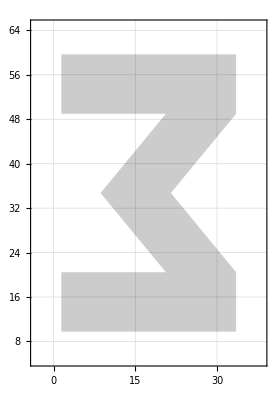
{З,-Graphics-,{{1.4256,59.6727},{33.5016,59.6727},{33.5016,48.9807},{21.5288,34.7247},{33.5016,20.4687},{33.5016,9.77672},{1.4256,9.77672},{1.4256,20.4687},{20.6044,20.4687},{8.62043,34.7247},{20.6044,48.9807},{1.4256,48.9807}}}

```mathematica
{Letter,FigLetter,Vertices}=Apply[{First@#1,Uncompress@Last@#1,{##2}}&,Import["NG22P01Problem.xlsx",{"Sheets","ГолубовичР"}]]
```

```mathematica
s = Length[Vertices]
```

12

```mathematica
Manipulate[Show[FigLetter, Graphics[{Red, AbsolutePointSize[10], Point[Vertices], Black,MapThread[Text[#1,#2]&, {Range[s], Vertices+1.2}],Blue, Opacity[0.5],HalfPlane[{Vertices[[Mod[i+1,s,1]]], Vertices⟦i⟧}, {{0,-1},{1,0}}.Vertices⟦Mod[i+1,s,1]⟧-{{0,-1},{1,0}}.Vertices⟦i⟧]}],PlotLabel->Style[ToString[Mod[i+1,s,1]]<>"->"<>ToString[i]]], {{i,1, "Полуплоскость"},Range[s]}, ControlType->SetterBar]
```

Range::range: Range specification in Range[s] does not have appropriate bounds.

MapThread::mptd: Object Range[s] at position {2, 1} in MapThread[Text[#1,#2]&,{Range[s],1.2+Vertices}] has only 0 of required 1 dimensions.

Part::pkspec1: The expression Mod[2,s,1] cannot be used as a part specification.

Part::partd: Part specification Vertices⟦1⟧ is longer than depth of object.

Part::pkspec1: The expression Mod[2,s,1] cannot be used as a part specification.

Part::partd: Part specification Vertices⟦1⟧ is longer than depth of object.

Show::gcomb: Could not combine the graphics objects in Show[FigLetter,,PlotLabel→Mod[2, s, 1]->1].

Range::range: Range specification in Range[s] does not have appropriate bounds.

MapThread::mptd: Object Range[s] at position {2, 1} in MapThread[Text[#1,#2]&,{Range[s],{{2.6256,60.8727},{34.7016,60.8727},{34.7016,50.1807},{22.7288,35.9247},{34.7016,21.6687},{34.7016,10.9767},{2.6256,10.9767},{2.6256,21.6687},{21.8044,21.6687},{9.82043,35.9247},{21.8044,50.1807},{2.6256,50.1807}}}] has only 0 of required 1 dimensions.

Part::pkspec1: The expression Mod[2,s,1] cannot be used as a part specification.

## Задание 2

```mathematica
allw1w2=Normalize[{{0,-1},{1,0}}.(Vertices[[Mod[#+1, s, 1]]]-Vertices[[#]])] &/@Range[s]
```

{{0.,1.},{1.,0.},{0.765764,-0.643122},{0.765764,0.643122},{1.,0.},{0.,-1.},{-1.,0.},{0.,1.},{-0.765469,-0.643473},{-0.765469,0.643473},{0.,-1.},{-1.,0.}}

```mathematica
allw0 = -allw1w2[[#]].Vertices[[#]]&/@Range[s]
```

{-59.6727,-33.5016,5.84626,-38.8182,-33.5016,9.77672,1.4256,-20.4687,28.9431,-15.7457,48.9807,1.4256}

```mathematica
innertable = MapThread[Join[#1, #2]&, {Table[{Mod[i+1, s, 1], i},{i, 1, s}], MapThread[{Flatten[#1, 2],#2}&, {allw1w2,allw0}]}]//Flatten[#]&//Partition[#, 5]&;
```

```mathematica
weights = innertable[[All,3;;]]
```

{{0.,1.,-59.6727},{1.,0.,-33.5016},{0.765764,-0.643122,5.84626},{0.765764,0.643122,-38.8182},{1.,0.,-33.5016},{0.,-1.,9.77672},{-1.,0.,1.4256},{0.,1.,-20.4687},{-0.765469,-0.643473,28.9431},{-0.765469,0.643473,-15.7457},{0.,-1.,48.9807},{-1.,0.,1.4256}}

```mathematica
totaltable = Join[{{"From","To","W1","W2","W0"} },innertable];
```

```mathematica
Export["NG4P01 ГолубовичРоман.xlsx","Layer1"->totaltable, "FormattedData"]
```

NG4P01 ГолубовичРоман.xlsx

```mathematica
kmANN[W_List]:= Sign[W.Append[#,1]]&
```

```mathematica
Manipulate[Show[FigLetter,Graphics[{Red, AbsolutePointSize[10], Point[Vertices], Black,MapThread[Text[#1,#2]&, {Range[s], Vertices+1.2}]}],DensityPlot[kmANN[weights[[i]]]@{x,y},{x,Min[Vertices[[All, 1]]]-5, Max[Vertices[[All, 1]]]+5},{y,Min[Vertices[[All, 2]]]-5, Max[Vertices[[All, 2]]]+5},ColorFunctionScaling->False,
 ColorFunction->(Piecewise[{{Opacity[0,Blue], #<0}, {Opacity[0.3,Blue], #>0}, {Blue, True}}]&)],PlotLabel->ToString@Subscript["W1,",ToString[1]]<>ToString@weights[[1]]],{{i,1, "Нейрон"},Range[s]}, ControlType->SetterBar]
```

## Задание 3

```mathematica
Manipulate[DynamicModule[{p={20,50}},LocatorPane[Dynamic@p,Show[FigLetter,Graphics[Locator[Dynamic[p]]],Graphics[{Locator[Dynamic[p]],Red, AbsolutePointSize[10], Point[Vertices], Black,MapThread[Text[#1,#2]&, {Range[s], Vertices+1.2}]}],DensityPlot[kmANN[weights[[i]]]@{x,y},{x,Min[Vertices[[All, 1]]]-5, Max[Vertices[[All, 1]]]+5},{y,Min[Vertices[[All, 2]]]-5, Max[Vertices[[All, 2]]]+5},ColorFunctionScaling->False,
 ColorFunction->(Piecewise[{{Opacity[0,Blue], #<0}, {Opacity[0.3,Blue], #>0}, {Blue, True}}]&)],Background->Style[Blue],PlotLabel->Style[Dynamic@Grid[{Range[s],kmANN[weights]@p/.{-1->Style[-1,Red],1->Style[1,Blue]}},Frame->All,Background->{{i->Yellow},None}],Bold]]]],{{i,1, "Нейрон первого слоя"},Range[s]}, ControlType->SetterBar]
```

## Задание 4

```mathematica
reg1 ={-1,-1,0,0,0,0,0,0,0,0,-1,-1,c1}
```

{-1,-1,0,0,0,0,0,0,0,0,-1,-1,c1}

```mathematica
reg2 = {0,0,0,0,-1,-1,-1,-1,0,0,0,0,c2}
```

{0,0,0,0,-1,-1,-1,-1,0,0,0,0,c2}

```mathematica
reg3 = {0,0,-1,0,0,0,0,0,-1,-1,1,0,c3}
```

{0,0,-1,0,0,0,0,0,-1,-1,1,0,c3}

```mathematica
reg4 = {0,0,0,-1,0,0,0,1,-1,-1,0,0,c4}
```

{0,0,0,-1,0,0,0,1,-1,-1,0,0,c4}

```mathematica
regs = {reg1,reg2,reg3,reg4}
```

{{-1,-1,0,0,0,0,0,0,0,0,-1,-1,c1},{0,0,0,0,-1,-1,-1,-1,0,0,0,0,c2},{0,0,-1,0,0,0,0,0,-1,-1,1,0,c3},{0,0,0,-1,0,0,0,1,-1,-1,0,0,c4}}

```mathematica
s2=Length@regs
```

4

```mathematica
(kmANN[regs]@kmANN[weights]@{15,35})[[4]]
```

Sign[4+c4]

```mathematica
c1=-3;
```

```mathematica
c2=-3;
c3=-3;
c4=-3;
```

```mathematica
Manipulate[Show[FigLetter,Graphics[{Red, AbsolutePointSize[10], Point[Vertices], Black,MapThread[Text[#1,#2]&, {Range[s], Vertices+1.2}]}],DensityPlot[(kmANN[regs]@kmANN[weights]@{x,y})[[i]],{x,Min[Vertices[[All, 1]]]-50, Max[Vertices[[All, 1]]]+50},{y,Min[Vertices[[All, 2]]]-50, Max[Vertices[[All, 2]]]+50},ColorFunctionScaling->False,
 ColorFunction->(Piecewise[{{Opacity[0,Blue], #<0}, {Opacity[0.3,Blue], #>0}, {Blue, True}}]&)]],{{i,1,"Многоугольник"},Range[s2]},ControlType->Setter]
```

## Задание 5

```mathematica
shapka =Join[ {"Polygon"},Table["W"<>ToString@Mod[i,s+1],{i,s+1}]]
```

{Polygon,W1,W2,W3,W4,W5,W6,W7,W8,W9,W10,W11,W12,W0}

```mathematica
names = {{"!#1 && !#2 && !#11 && !#12&"},{"!#5 && !#6 && !#7 && !#8&"},{"!#3 && !#9 && !#10 && #11&"},{"!#4 && #8 && !#9 && !#10&"}}
```

{{!#1 && !#2 && !#11 && !#12&},{!#5 && !#6 && !#7 && !#8&},{!#3 && !#9 && !#10 && #11&},{!#4 && #8 && !#9 && !#10&}}

```mathematica
innertable2 = MapThread[Flatten[Join[#1,#2],1]&,{names,regs}]
```

{{!#1 && !#2 && !#11 && !#12&,-1,-1,0,0,0,0,0,0,0,0,-1,-1,-3},{!#5 && !#6 && !#7 && !#8&,0,0,0,0,-1,-1,-1,-1,0,0,0,0,-3},{!#3 && !#9 && !#10 && #11&,0,0,-1,0,0,0,0,0,-1,-1,1,0,-3},{!#4 && #8 && !#9 && !#10&,0,0,0,-1,0,0,0,1,-1,-1,0,0,-3}}

```mathematica
totaltable2 = Join[{shapka},innertable2]
```

{{Polygon,W1,W2,W3,W4,W5,W6,W7,W8,W9,W10,W11,W12,W0},{!#1 && !#2 && !#11 && !#12&,-1,-1,0,0,0,0,0,0,0,0,-1,-1,-3},{!#5 && !#6 && !#7 && !#8&,0,0,0,0,-1,-1,-1,-1,0,0,0,0,-3},{!#3 && !#9 && !#10 && #11&,0,0,-1,0,0,0,0,0,-1,-1,1,0,-3},{!#4 && #8 && !#9 && !#10&,0,0,0,-1,0,0,0,1,-1,-1,0,0,-3}}

```mathematica
Export["NG4P01 ГолубовичРоман.xlsx",{"Layer1"->totaltable,"Layer2"->totaltable2},"FormattedData"]
```

NG4P01 ГолубовичРоман.xlsx

```mathematica
Manipulate[DynamicModule[{p={20,50}},LocatorPane[Dynamic@p,Show[FigLetter,Graphics[{Red, AbsolutePointSize[10], Point[Vertices], Black,MapThread[Text[#1,#2]&, {Range[s], Vertices+1.2}]}],DensityPlot[(kmANN[regs]@kmANN[weights]@{x,y})[[i]],{x,Min[Vertices[[All, 1]]]-50, Max[Vertices[[All, 1]]]+50},{y,Min[Vertices[[All, 2]]]-50, Max[Vertices[[All, 2]]]+50},ColorFunctionScaling->False,
 ColorFunction->(Piecewise[{{Opacity[0,Blue], #<0}, {Opacity[0.3,Blue], #>0}, {Blue, True}}]&)],PlotLabel->Style[Dynamic@Grid[{Range[s2],kmANN[regs]@kmANN[weights]@p/.{-1->Style[-1,Red],1->Style[1,Blue]}},Frame->All,Background->{{i->Yellow},None}],Bold]]]],{{i,1,"Нейрон второго слоя"},Range[s2]},ControlType->Setter]
```

## Задание 6

```mathematica
finalneyron = {1,1,1,1,c0}
```

{1,1,1,1,c0}

```mathematica
s3=Length@finalneyron
```

5

```mathematica
kmANN[finalneyron]@kmANN[regs]@kmANN[weights]@{20,15}
```

Sign[-2+c0]

```mathematica
c0=3;
```

```mathematica
Manipulate[Show[FigLetter,Graphics[{Locator[Dynamic[p]],Red, AbsolutePointSize[10], Point[Vertices], Black,MapThread[Text[#1,#2]&, {Range[s], Vertices+1.2}]}],PlotLabel->kmANN[finalneyron]@kmANN[regs]@kmANN[weights]@p/.{1->Style[p,Blue],-1->Style[p,Red]}],{{p,{20,35}},Locator}]
```

```mathematica
shapka = {"Polygon",Sequence@@Table["W"<>ToString@Mod[i, s3],{i,s3}]}
```

{Polygon,W1,W2,W3,W4,W0}

```mathematica
names = {"#1 && #2 && #3 && #4&"}
```

{#1 && #2 && #3 && #4&}

```mathematica
innertable3 = Join[names,finalneyron]
```

{#1 && #2 && #3 && #4&,1,1,1,1,3}

```mathematica
totaltable3 = {shapka,innertable3}
```

{{Polygon,W1,W2,W3,W4,W0},{#1 && #2 && #3 && #4&,1,1,1,1,3}}

```mathematica
Export["NG4P01 ГолубовичРоман.xlsx",{"Layer1"->totaltable,"Layer2"->totaltable2,"Layer3"->totaltable3},"FormattedData"]
```

NG4P01 ГолубовичРоман.xlsx